## Constantes

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

## Concentración 28.7 g/dL

```mathematica
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
datosH2ORe=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\H2O_n.csv"];
datosH2OIm=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\H2O_k.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
datos1H2ORe=Drop[datosH2ORe,1];
datos1H2OIm=Drop[datosH2OIm,1];
datos2H2OIm=h c /(datos1H2OIm[[All,1]]*1000);
datos2H2ORe=h c/(datos1H2ORe[[All,1]]*1000);
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}]];
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]];
h2oRe=Interpolation[Transpose[{datos2H2ORe,datos1H2ORe[[All,2]]}]];
h2oIm=Interpolation[Transpose[{datos2H2OIm,datos1H2OIm[[All,2]]}]];
(*Se toma a la primera columna como el vector de energía*)
```

```mathematica
eps1[x_]:=parteRe[x]^2-parteIm[x]^2;
eps2[x_]:=(2*parteRe[x]*parteIm[x]);
eps1h2o[x_]:=h2oRe[x]^2-h2oIm[x]^2;
eps2h2o[x_]:=(2*h2oRe[x]*h2oIm[x]);
resta[x_]:=eps1[x]-eps1h2o[x];
```

```mathematica
parteIm1=Table[eps2[x],{x,1.19,4.82,0.01}];
parteRe1=Table[eps1[x],{x,1.19,4.82,0.01}];
parteReH2O=Table[eps1h2o[x],{x,1.19,4.82}];
parteImH2O=Table[eps2h2o[x],{x,1.19,4.82}];
energias=Range[1.19,4.82,0.01];
```

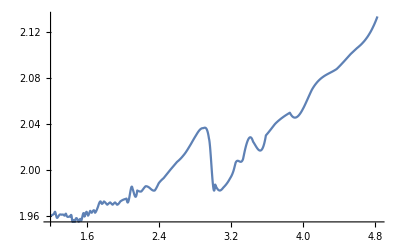

```mathematica
Plot[{eps1[x]},{x,1.19,4.83},PlotRange->All]
```

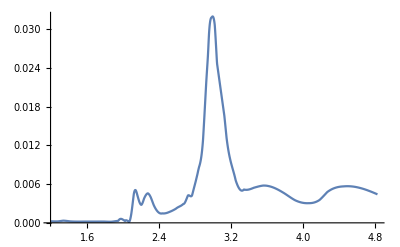

```mathematica
Plot[{eps2[x]},{x,1.19,4.83},PlotRange->All]
```

```mathematica
GoldenSearchMax[eps2,2.1,2.2]
GoldenSearchMax[eps2,2.2,2.4]
GoldenSearchMax[eps2,2.8,3.3]
GoldenSearchMax[eps2,3.5,3.8]
GoldenSearchMax[eps2,4,4.7]
```

2.13396

2.27349

2.99459

3.56451

4.49601

Ahora se van a ajustar las funciones con lorentzianas

InterpolatingFunction::dmval: Input value {4.83329} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84329} lies outside the range of data in the interpolating function. Extrapolation will be used.

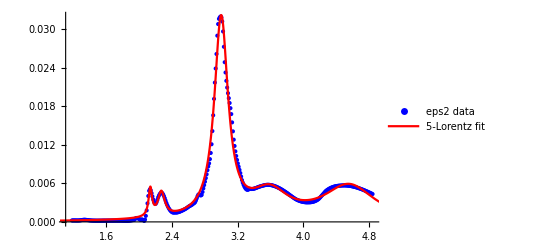

```mathematica
xmin=Min[datos2Im];
xmax=Max[datos2Im];
(* ==3. Datos para ajuste==*)
eps2Data=Table[{x,eps2[x]},{x,xmin,xmax,0.01}];

(* ==4. Definir suma de 5 Lorentzianas imaginarias==*)
lorentz[ω_,ω0_,γ_]:=(γ/2)^2/((ω-ω0)^2+(γ/2)^2)

lorentzSum[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentz[ω,ω01,γ1]+A2 lorentz[ω,ω02,γ2]+A3 lorentz[ω,ω03,γ3]+A4 lorentz[ω,ω04,γ4]+A5 lorentz[ω,ω05,γ5];

(* ==5. Ajustar con NonlinearModelFit==*)
fit=NonlinearModelFit[eps2Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,2.15},{γ1,0.1},{A2,0.01},{ω02,2.3},{γ2,0.1},{A3,0.01},{ω03,3.05},{γ3,0.1},{A4,0.01},{ω04,3.65},{γ4,0.1},{A5,0.01},{ω05,4.35},{γ5,0.1}},ω];

(* ==6. Graficar datos originales y ajuste con 5 Lorentzianas==*)
Show[ListPlot[eps2Data,PlotStyle->Blue,PlotLegends->{"eps2 data"},PlotRange->All],Plot[fit[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"5-Lorentz fit"},PlotRange->All]]
```

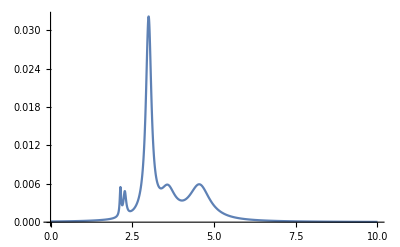

```mathematica
Plot[fit[ω],{ω,0,10},PlotRange->All]
```

```mathematica
eri=Table[fit[x],{x,0,10,0.01}];
omega=Range[0,10,0.01];
```

```mathematica
parteReKK1=kkrebook[omega,eri];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0.000101259.

Set::setraw: Cannot assign to raw object 0.000101824.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

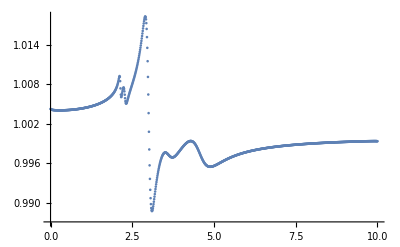

```mathematica
ListPlot[Transpose[{omega,parteReKK1}],PlotRange->All]
```

## Valores de 32 g/dL

```mathematica
datos0re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\32_n_ReN_Erythrocytes.csv"];
datosuA=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\32_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1re=Drop[datos0re,1];
datos1uA=Drop[datosuA,1];
datos2re=h c/datos1re[[All,1]];
datos2im=h c/datos1uA[[All,1]];
datos3im=datos1uA[[All,2]]*10^(-6)*datos1uA[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteRe32=Interpolation[Transpose[{datos2re,datos1re[[All,2]]}]];
parteIm32=Interpolation[Transpose[{datos2im,datos3im}]];
(*Se toma a la primera columna como el vector de energía*)
```

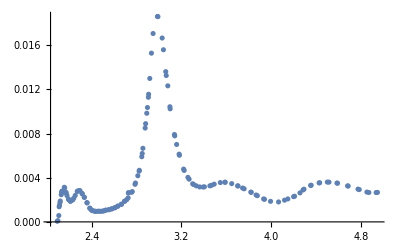

```mathematica
ListPlot[Transpose[{datos2im,datos3im}],PlotRange->All]
```

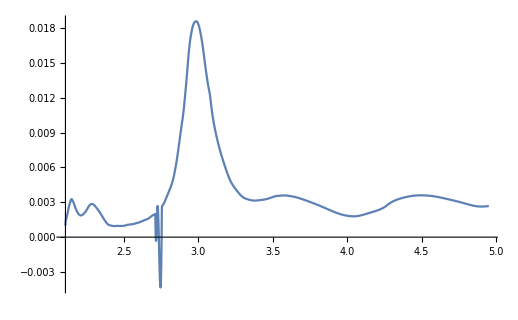

```mathematica
Plot[parteIm32[x],{x,2.11,4.95},PlotRange->All]
```

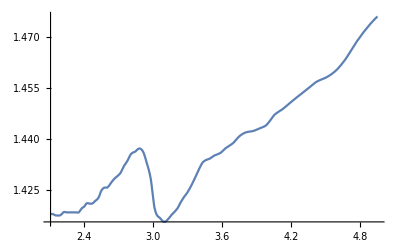

```mathematica
Plot[parteRe32[x],{x,2.11,4.95}]
```

```mathematica
eps132[x_]:=parteRe32[x]^2-parteIm32[x]^2;
eps232[x_]:=(2*parteRe32[x]*parteIm32[x]);
```

```mathematica
eps232[3]
```

0.0398795

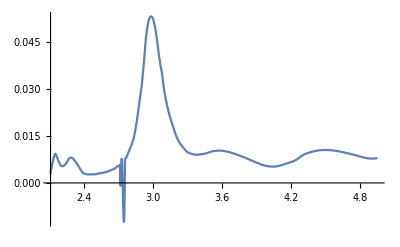

```mathematica
Plot[eps232[x],{x,2.11,4.95},PlotRange->All]
```

```mathematica
GoldenSearchMax[eps2,2,2.1]
GoldenSearchMax[eps2,2.15,2.3]
GoldenSearchMax[eps2,2.8,3.2]
GoldenSearchMax[eps2,3.4,3.7]
GoldenSearchMax[eps2,4.2,4.7]
```

2.03224

2.27349

2.99459

3.56451

4.49601

Ahora se van a ajustar las funciones con lorentzianas

InterpolatingFunction::dmval: Input value {4.94724} lies outside the range of data in the interpolating function. Extrapolation will be used.

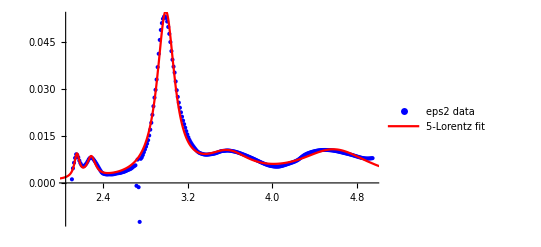

```mathematica
xmin32=Min[datos2im];
xmax32=Max[datos2im];
(* ==3. Datos para ajuste==*)
eps2Data32=Table[{x,eps232[x]},{x,2.1072428004395536,4.947483825276942,0.01}];
(* ==5. Ajustar con NonlinearModelFit==*)
fit32=NonlinearModelFit[eps2Data32,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,2.03223842616458},{γ1,0.1},{A2,0.01},{ω02,2.273493961758059},{γ2,0.1},{A3,0.01},{ω03,2.9945906484705747},{γ3,0.01},{A4,0.01},{ω04,3.5645078249270967},{γ4,0.1},{A5,0.01},{ω05,4.496008473348992},{γ5,0.1}},ω];

(* ==6. Graficar datos originales y ajuste con 5 Lorentzianas==*)
Show[ListPlot[eps2Data32,PlotStyle->Blue,PlotLegends->{"eps2 data"},PlotRange->All],Plot[fit32[ω],{ω,xmin32-0.5,xmax32+0.5},PlotStyle->{Thick,Red},PlotLegends->{"5-Lorentz fit"},PlotRange->All]]
```

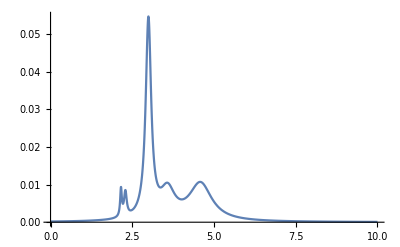

```mathematica
Plot[fit32[ω],{ω,0,10},PlotRange->All]
```

```mathematica
eri32=Table[fit32[x],{x,0,10,0.01}];
omega=Range[0,10,0.01];
parteReKK32=kkrebook[omega,eri32];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0.000188314.

Set::setraw: Cannot assign to raw object 0.000189343.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

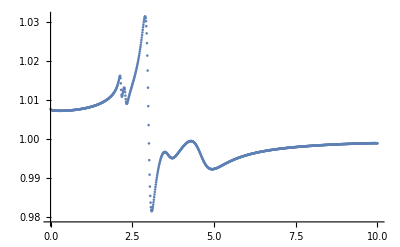

```mathematica
ListPlot[Transpose[{omega,parteReKK32}],PlotRange->All]
```

## Valores de 30.6 g/dL

```mathematica
datos0re30=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\30.6_n_ReN_Erythrocytes.csv"];
datosuA30=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1re30=Drop[datos0re30,1];
datos1uA30=Drop[datosuA30,1];
datos2re30=h c/datos1re30[[All,1]];
datos2im30=h c/datos1uA30[[All,1]];
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteRe30=Interpolation[Transpose[{datos2re30,datos1re30[[All,2]]}]];
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],Method->"Spline"];
(*Se toma a la primera columna como el vector de energía*)
```

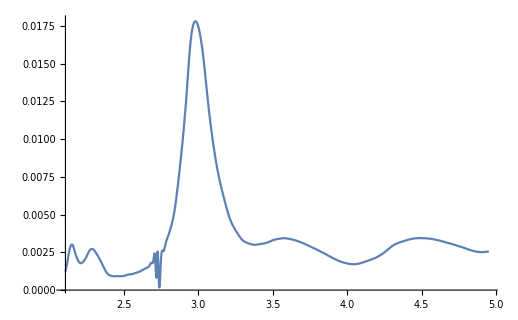

```mathematica
Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
```

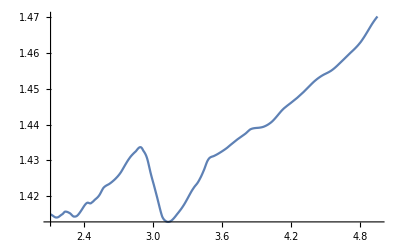

```mathematica
Plot[parteRe30[x],{x,2.11,4.95}]
```

```mathematica
eps130[x_]:=parteRe30[x]^2-parteIm30[x]^2;
eps230[x_]:=(2*parteRe30[x]*parteIm30[x]);
```

Ahora se van a ajustar las funciones con lorentzianas

```mathematica
GoldenSearchMax[eps2,2,2.1]
GoldenSearchMax[eps2,2.15,2.4]
GoldenSearchMax[eps2,2.8,3.2]
GoldenSearchMax[eps2,3.4,3.7]
GoldenSearchMax[eps2,4.2,4.7]
```

2.03224

2.27349

2.99459

3.56451

4.49601

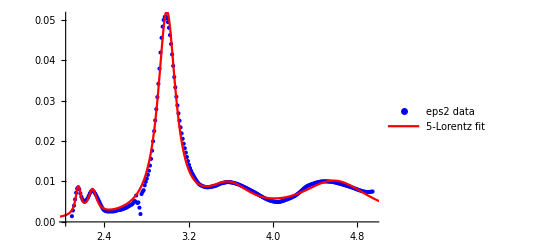

```mathematica
xmin30=Min[datos2im30];
xmax30=Max[datos2im30];
(* ==3. Datos para ajuste==*)
eps2Data30=Table[{x,eps230[x]},{x,xmin30,xmax30,0.01}];

(* ==5. Ajustar con NonlinearModelFit==*)
fit30=NonlinearModelFit[eps2Data30,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,2.05},{γ1,0.05},{A2,0.01},{ω02,2.275},{γ2,0.1},{A3,0.01},{ω03,3},{γ3,0.1},{A4,0.01},{ω04,3.55},{γ4,0.05},{A5,0.01},{ω05,4.45},{γ5,0.1}},ω];

(* ==6. Graficar datos originales y ajuste con 5 Lorentzianas==*)
Show[ListPlot[eps2Data30,PlotStyle->Blue,PlotLegends->{"eps2 data"},PlotRange->All],Plot[fit30[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"5-Lorentz fit"},PlotRange->All]]
```

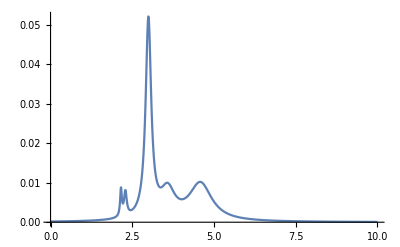

```mathematica
Plot[fit30[ω],{ω,0,10},PlotRange->All]
```

```mathematica
eri30=Table[fit30[x],{x,0,10,0.01}];
omega=Range[0,10,0.01];
```

```mathematica
parteReKK30=kkrebook[omega,eri30];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0.000181009.

Set::setraw: Cannot assign to raw object 0.000182001.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

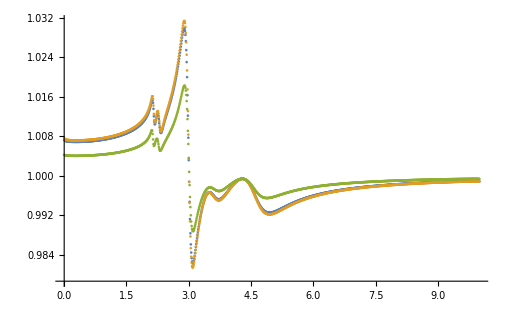

```mathematica
ListPlot[{Transpose[{omega,parteReKK30}],Transpose[{omega,parteReKK32}],Transpose[{omega,parteReKK1}]},PlotRange->All]
```